## MAT 331: Homework 2

## Problem 2.1

In this problem we will explore some of the basic definitions and Mathematica functions for graphs. A walk in a graph consists of an alternating sequence of vertices and edges x_0, e_1, x_1,.., e_n, x_n such that e_i=x_(i-1)→x_i is an edge between vertex x_(i-1)and vertex x_i. A walk is closed if x_0=x_n and open otherwise. The number of edges is the length of a walk. The vertices and edges may be repeated in a walk. A path is (usually defined as) an open walk with no repeated vertices. A cycle is a closed walk with no repeated vertices, other than the first and last vertex. The problem of finding the shortest path between two vertices is very relevant to practical problems, such as finding the way out of a maze or navigating a road network. Cycles are also very important if traversing the whole graph in some way and coming back to the same place is desired instead. 
Another relevant feature of graphs representing real systems is community structure, or clustering, i. e. the organization of vertices in clusters, with many edges joining vertices of the same cluster and comparatively few edges joining vertices of different clusters. Such clusters, or communities, can be considered as fairly independent compartments of a graph, playing a similar role like, e. g., the tissues or the organs in the human body. Detecting communities is of great importance in sociology, biology and computer science, disciplines where systems are often represented as graphs.

Consider the directed graph G depicted below (you may need to click on Enable Dynamics first, to view the graph):

Use the function Graph[...] to generate the graph G. The option GraphStyle→”SmallNetwork” will give the same display style as above, but you are free to explore additional attributes as well.

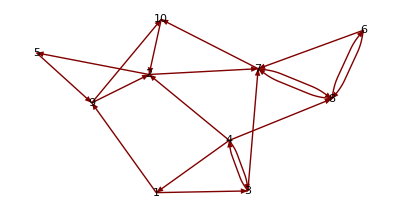

```mathematica
GraphPlot[{1->3,1->9,2->5,2->7,3->4,3->7,4->1,4->2,4->3,4->8,5->9,6->7,6->8,7->8,7->10,8->6,8->7,9->2,9->10,10->2},DirectedEdges->True,VertexLabeling->True]
```

Professor, I try to use G=Graph[{1→3,1→9,2→5,2→7,3→4,3→7,4→1,4→2,4→3,4→8,5→9,6→7,6→8,7→8,7→10,8→6,8→7,9→2,9→10,10→2}];
Gplot=GraphPlot[G,DirectedEdges→True,VertexLabeling→True]  this code, but the output contains wrong directions, I don’t know what’s wrong here.

Find the strongly connected components of G. Use HighlightGraph[...] to color the vertices of the graph according to the component they belong to.

```mathematica
G=Graph[{1->3,1->9,2->5,2->7,3->4,3->7,4->1,4->2,4->3,4->8,5->9,6->7,6->8,7->8,7->10,8->6,8->7,9->2,9->10,10->2}];
ConnectedComponents[G]
HighlightGraph[G,ConnectedComponents[G]]
```

{{9,2,5,7,8,6,10},{1,3,4}}

-Graphics-

Use the function FindGraphCommunities[...] to find a list of communities in the graph G. This function returns a list of communities, where each community is a list of vertices. The communities are ordered by their length, with the largest community first. Use the command HighlightGraph[...] to color the vertices of the graph according to the community they belong to.

{{9,2,5,10},{1,3,4},{7,8,6}}

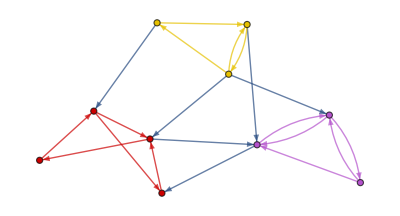

```mathematica
FindGraphCommunities[G]
HighlightGraph[G,Map[Subgraph[G,#]&,%]]
```

ShortestPath[G, v1, v2] returns a list of vertices representing the shortest path between nodes v1 and v2. Use this function to find the shortest path between node 6 and node 9 and then use HighlightGraph[...] to highlight the shortest path between these nodes. First highlight only the vertices, then highlight the edges of the shortest path. Use GraphicsRow[...] to print the two highlighted graphs on the same row.

```mathematica
G=Graph[{1->3,1->9,2->5,2->7,3->4,3->7,4->1,4->2,4->3,4->8,5->9,6->7,6->8,7->8,7->10,8->6,8->7,9->2,9->10,10->2}]
```

```mathematica
FindShortestPath[G, 6, 9]
```

{6,7,10,2,5,9}

```mathematica
HighlightGraph[G,{6,7,10,2,5,9}]
```

-Graphics-

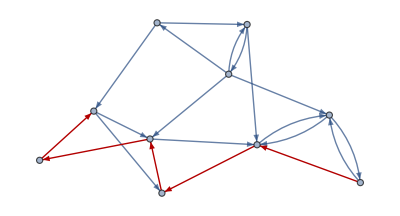

```mathematica
HighlightGraph[G,{6->7,7->10,10->2,2->5,5->9}]
```

```mathematica
GraphicsRow[{HighlightGraph[G,{6,7,10,2,5,9}],HighlightGraph[G,{6->7,7->10,10->2,2->5,5->9}]}]
```

-Graphics-

GraphDiameter[G] gives the greatest distance between any pair of vertices in the graph G. What is the diameter of G? Explain.

```mathematica
GraphDiameter[Graph[{1,2,3,4,5,6,7,8,9,10},{{1,3},{1,9},{2,5},{2,7},{3,4},{3,7},{4,1},{4,2},{4,3},{4,8},{5,9},{6,7},{6,8},{7,8},{7,10},{8,6},{8,7},{9,2},{9,10},{10,2}}]]
```

3

I don’t think 3 will be the answer, but it is what I got.....

Diameter is  the greatest distance between any pair of vertices in the graph G.

## Problem 2.2

Consider the graph G from problem 2.1. The command FindCycle[G,{n}] returns a cycle of length n in graph G. Use this function to find a cycle of length 3 in G. Suppose next that we want to find all cycles of length 3 in G. There are several ways to do that, but we will choose to work with the adjacency matrix of G for this task. Use your prefered loop structures in Mathematica (Do, While, For) to find how many cycles of length exactly 3 are in the graph G and to print all of these cycles. A cycle should be displayed as a list of edges of the form {a→b, b→c, c→a}. Do not print the same cycle three times! For example, {a→b, b→c, c→a}, {b→c, c→a, a→b}, {c→a, a→b, b→c} are different ways of writing the same cycle, which should be counted only once.

```mathematica
g=Graph[{1->3,1->9,2->5,2->7,3->4,3->7,4->1,4->2,4->3,4->8,5->9,6->7,6->8,7->8,7->10,8->6,8->7,9->2,9->10,10->2}]
```

-Graphics-

```mathematica
FindCycle[g,{3}]
```

{{1->3,3->4,4->1}}

```mathematica
FindCycle[g,{3},All]
```

{{7->8,8->6,6->7},{2->7,7->10,10->2},{9->2,2->5,5->9},{1->3,3->4,4->1}}

```mathematica
Adj=MatrixForm[AdjacencyMatrix[g]]
```

(0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
For[i=1;i≤10;i++,For[j=1,j≤10,If[Adj[i,j]=Adj[j,k]=1,{i->j}]]
Print[{i->j}]
```

Syntax::bktmcp: Expression "For[i=1;i≤10;i++,For[j=1,j≤10,If[Adj[i,j]=Adj[j,k]=1,{i->j}]]Print[{i->j}]" has no closing "]".

## Problem 2.3

Write a function transition[...] that takes as input a directed graph H with any number of nodes, represented as a list of directed edges, and returns the transition matrix of H. Recall that the (i,j) entry of the transition matrix reflects the probability of transition from node i to node j. A preliminary version of the algorithm for computing the transition matrix of a graph is done is the lecture notes. There are some special cases which were not covered in the lecture (like the case of nodes with no outgoing edges). Test your function on the graph from problem 1, as well as on randomly generated graphs.

```mathematica
g=Graph[{1->3,1->9,2->5,2->7,3->4,3->7,4->1,4->2,4->3,4->8,5->9,6->7,6->8,7->8,7->10,8->6,8->7,9->2,9->10,10->2}]
Lin= VertexInDegree[g]; 
Print["Lin=",Lin]
Lout=VertexOutDegree[g]; 
Print["Lout=",Lout]
```

-Graphics-

Lin={1,2,2,3,1,4,1,3,1,2}

Lout={2,2,2,2,1,2,4,2,2,1}

```mathematica
A=AdjacencyMatrix[g];
TA = Transpose[A];
Print["The transpose matrix is TA="MatrixForm[TA]]
```

The transpose matrix is TA= (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
f[i_,j_]:=TA[[i]][[j]]/Lout[[j]]
Trans= Table[f[i,j],{i,Length[TA]},{j,Length[TA]}];
MatrixForm[Trans]
```

(0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 1/2 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 1/4 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0)

```mathematica
k=RandomGraph[{4,8},DirectedEdges->True]
```

-Graphics-

```mathematica
Lin= VertexInDegree[k]; 
Print["Lin=",Lin]
Lout=VertexOutDegree[k]; 
Print["Lout=",Lout]
```

Lin={2,3,1,2}

Lout={2,1,3,2}

```mathematica
B=AdjacencyMatrix[g];
TaT = Transpose[B];
Print["The transpose matrix is TaT="MatrixForm[TaT]]
```

The transpose matrix is TaT= (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
f[i_,j_]:=TaT[[i]][[j]]/Lout[[j]]
Trans= Table[f[i,j],{i,Length[TaT]},{j,Length[TaT]}];
MatrixForm[Trans]
```

(0 | 0 | 0 | 0 | 0 | 0 | 1/({2,1,3,2}⟦7⟧) | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 1/({2,1,3,2}⟦7⟧) | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 1/({2,1,3,2}⟦5⟧) | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/3 | 0 | 0 | 0 | 1/({2,1,3,2}⟦7⟧) | 0 | 0 | 1/({2,1,3,2}⟦10⟧)
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1/2 | 0 | 0 | 0 | 1/({2,1,3,2}⟦8⟧) | 1/({2,1,3,2}⟦9⟧) | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/({2,1,3,2}⟦6⟧) | 1/({2,1,3,2}⟦7⟧) | 0 | 1/({2,1,3,2}⟦9⟧) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/({2,1,3,2}⟦8⟧) | 0 | 0
0 | 0 | 1/3 | 0 | 0 | 1/({2,1,3,2}⟦6⟧) | 0 | 0 | 0 | 0)

## Problem 2.4

Show that the following properties (1-3) hold true for any square nxn matrix A. If you have taken a course of linear algebra, show also part 4.

If λ is an eigenvalue of A, then λ^n is an eigenvalue of A^n.

```mathematica
A=Table[RandomInteger[],{i,4},{j,4}];
MatrixForm[A]
```

(1 | 1 | 0 | 1
0 | 1 | 1 | 0
1 | 1 | 0 | 1
0 | 1 | 1 | 0)

```mathematica
Eigenvalues[A]
```

{1+√2,1-√2,0,0}

```mathematica
({{1, 1, 0, 1}, {0, 1, 1, 0}, {1, 1, 0, 1}, {0, 1, 1, 0}}).({{1, 1, 0, 1}, {0, 1, 1, 0}, {1, 1, 0, 1}, {0, 1, 1, 0}})
```

{{1,3,2,1},{1,2,1,1},{1,3,2,1},{1,2,1,1}}

```mathematica
B={{1,3,2,1},{1,2,1,1},{1,3,2,1},{1,2,1,1}}
```

```mathematica
Eigenvalues[B]
```

{3+2 √2,3-2 √2,0,0}

B=A^2   check λ(B)=λ(A)^2

```mathematica
{1+√2,1-√2,0,0}.{1+√2,1-√2,0,0}={3+2 √2,3-2 √2,0,0}
```

yes, λ(B)=λ(A)^2

```mathematica
({{1, 1, 0, 1}, {0, 1, 1, 0}, {1, 1, 0, 1}, {0, 1, 1, 0}}).({{1, 1, 0, 1}, {0, 1, 1, 0}, {1, 1, 0, 1}, {0, 1, 1, 0}}).({{1, 1, 0, 1}, {0, 1, 1, 0}, {1, 1, 0, 1}, {0, 1, 1, 0}})
```

{{3,7,4,3},{2,5,3,2},{3,7,4,3},{2,5,3,2}}

```mathematica
K={{3,7,4,3},{2,5,3,2},{3,7,4,3},{2,5,3,2}}
```

```mathematica
Eigenvalues[K]
```

{7+5 √2,7-5 √2,0,0}

K=A^3   check λ(K)=λ(A)^3
{7+5 √2,7-5 √2,0,0}.{7+5 √2,7-5 √2,0,0}.{7+5 √2,7-5 √2,0,0}={7+5 √2,7-5 √2,0,0}
yes, λ(K)=λ(A)^3
So If λ is an eigenvalue of A, then λ^n is an eigenvalue of A^n.

A is invertible if and only if λ=0 is not an eigenvalue of A.

1) Assume A is not invertible. Then Ax = 0 does not have only trivial solution by invertible matrix theorem.
Since it does have the trivial solution (letting x = 0 gives a solution), but not only the trivial solution, there must be some other
solution. Thus the equation Ax = 0 = 0x has a nontrivial solution, so by definition, 0 is an eigenvalue.
 2) Assume 0 is an eigenvalue. Thus there is some nontrivial solution to Ax = 0x = 0. By the invertible matrix
theorem, if A was invertible there would only be the trivial solution. Since there in a nontrivial solution, it must be the case
that A is not invertible.

If A is invertible then 1/λ is an eigenvalue of A^-1.

```mathematica
A=({{1, 2}, {3, 4}});
Eigenvalues[A]
```

```mathematica
{1/2 (5+√33),1/2 (5-√33)}

Inverse[A]
```

```mathematica
{{-2,1},{3/2,-1/2}}
B={{-2,1},{3/2,-1/2}}
Eigenvalues[B]
```

```mathematica
{1/4 (-5-√33),1/4 (-5+√33)}
```

B is the inverse of A and λ(B)=1/λ(A)

If λ is an eigenvalue of A, then λ is also an eigenvalue of A^T.

Use the Basic Math Assistant Palette to write mathematical symbols. Your answer should be neatly formatted as text or as a numbered list.

If A is a square matrix, then its eigenvalues are equal to the eigenvalues of its transpose since they share the same Characteristic polynomial.

## Problem 2.5

Let H be any undirected graph. If H is a connected, acyclic graph (acyclic means that it contains no cycles) then we say that H is a tree. Trees are very useful for storing, sorting and quering information that has a natural hierarchical structure. For instance, the file system (folders, subfolders, documents, etc.) in a computer uses a tree architecture.

Show that a graph H is a tree if and only if any one of the following properties is satisfied:

Every pair of distinct vertices of H is connected by a unique path.

The graph H is connected, but deleting any edge disconnects H.

The graph H is acyclic, but adding any edge to H forms a cycle.

The graph H is connected and has n-1 edges, where n is the number of vertices of H.

To build some intuition about trees, use TreePlot[H, VertexLabeling→True, DirectedEdges→False] to plot any graph H which has the properties listed above. GraphPlot[...] can also be used for plotting trees, however the  layout is slightly different.

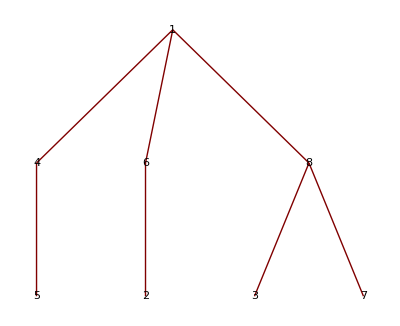

```mathematica
TreePlot[{1->4,1->6,1->8,2->6,3->8,4->5,7->8},VertexLabeling->True, DirectedEdges->False]
```

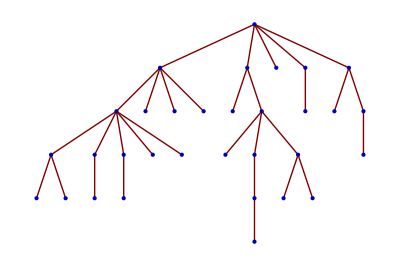

```mathematica
TreePlot[RandomInteger[#]->#+1&/@Range[0,30]]
```

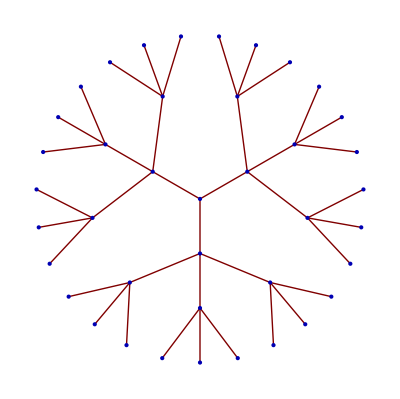

```mathematica
TreePlot[KaryTree[40,3],Center]
```

All graphs above are tree and they all satisfied properties 1,2,3 and4.

## Problem 2.6

In this problem, we want to use the command Manipulate[...] to create nice interactive models. We can wrap Manipulate[...] around any Wolfram command. The output you get from evaluating a Manipulate command is an interactive object containing one or more controls (sliders, etc.) that you can use to vary the value of one or more parameters.

RandomGraph[{m,n},k] generates k random undirected graphs with m vertices and n edges; if we want to generate directed graphs, we need to set the attribute DirectedEdges to True, as shown in the lecture notes. Your first task is to create a nice interactive model that can generate k (directed or undirected!) graphs with m vertices and (m(m-1))/2 edges. The possible values for k should be 1 and 4. The parameter m can be any positive integer between 4 and 10, with default value 6. You should have one extra parameter, called Directed, that can take the values True or False.

```mathematica
Manipulate[RandomGraph[{m,m*(m-1)/2},1,DirectedEdges->True],{m,4,10,1}]
```

```mathematica
Manipulate[RandomGraph[{m,m*(m-1)/2},4,DirectedEdges->True],{m,4,10,1}]
```

Let us now focus on part 4 of problem 2.1 and turn it into an interactive model as well. We do not want to change the graph G, but we would like to build an interactive model such that for any given choice of nodes v and u in G, we display the graph G with the shortest path between u and v highlighted. Use the command Manipulate[...] to create a nice interactive model with controls for the parameters u and v.

```mathematica
g=Graph[{1->3,1->9,2->5,2->7,3->4,3->7,4->1,4->2,4->3,4->8,5->9,6->7,6->8,7->8,7->10,8->6,8->7,9->2,9->10,10->2}]
```

-Graphics-

```mathematica
Manipulate[FindShortestPath[g, v, u],{v,1,10,1},{u,1,10,1}]
```

This code I need to hold v value and change u value.

```mathematica
g=Graph[{1->3,1->9,2->5,2->7,3->4,3->7,4->1,4->2,4->3,4->8,5->9,6->7,6->8,7->8,7->10,8->6,8->7,9->2,9->10,10->2}]
```

-Graphics-

```mathematica
Manipulate[HighlightGraph[g,PathGraph[FindShortestPath[g, v, u]]],{v,1,10,1},{u,1,10,1}]
```

I try my best but still can not color the edges.